## This program gives all roots of a compact graph with rationally dependent edges.

Run first to initialize. 
For each graph we have a matrix-valued function S(k) defined in many papers. Let mo be an adjacency matrix or a Graphobject (such as ). Graphobject variables should not have graphs with two vertices connected by two edges, such as  since the programs will then give the wrong results. The DeterminantD I get is often different from the  ∑(k) which is given in the literature and differs by a complex k-dependent factor, A ⅇ^(-ⅈ k) where A is real, which never contributes with a root.

GraphRoots[mo] returns all the roots (also called eigenfrequencies) of mo in an “exact” form, as long as the edges in the graph are rationally dependent. If they are not rationally dependent no solutions will be found. It finds the roots by constructing S(k), and then solving  ∑(k) = Det S(k) = 0 where ∑(k) is the secular determinant of the graph. The length of the graph is normalised to one. It is also possible to give two arguments:  GraphRoots[mo, L] in which case the length of the graph is set to L. 

NGraphRoots[mo] gives all the roots in a numeric form. Only one argument can be used, i. e. no length can be specified. If you want a length then use the command N@GraphRoots[mo, L].

NGraphRoots[mo, n], NGraphEigenvalues[mo, n] gives the n smallest roots and eigenvalues numerically. The eigenvalues of the graph are λ_n=k_n^2where k_n are the non-negative roots. The length cannot be given as an argument.

DeterminantD[mo] gives ∑(k), that is the determinant of S(k), and is very useful to inspect when determining the multiplicity of roots of a graphs. DeterminantD can also take a Graphobject as the variable. The length can be given as an argument, but is not well tested yet.

If GraphRoots has been run then S[k] is available as a function.

If you have parameters in your graph, c1, c2, c3 and c4 then GraphRoots, NGraphRoots and NGraphEigenvalues will still run but assume c1 = c2 = c3=1. GraphRoots will also construct S[k, c1, c2,c3], which is useful for numerical investigations. S[k] is a valid expression and in this case c1, c2, c3 and c4 have been set to 1.  

Det@S[k] is useful to get the secular determinant of a graph which contains two symbolic entries.

Due to bad programming the optional six free parameters in a graph must be labelled  c1, c2, c3, c4, c5, c6.

```mathematica
(*Remove["Global`*"];*)
x1=3;x2=3;eigs={0,1,2,3, 4, 5}; (* This values are just set to dummy values to make Dynamic sane in some programs using this program. It is only for cosmetic reasons. *)

GraphRoots[w_List|w_Graph,L_:1,solve_:1]:=Module[{n,s,t,m,mo,M,matn,eqns,vars,roots},Off[Part::pspec];Off[Part::pkspec1];
If[Head[w]==Graph,mo=(WeightedAdjacencyMatrix[w]//Normal)/.{0->∞},1];
If[Head[w]==List,mo=w,1];

m=mo/.{∞->0};

M=1/2*Plus@@(m//Flatten);
m= L m/M; (* We here set the length of the graph to M *)
n=mo/.{(n_/;n≠∞)->1,∞->0,c1->1,c2->1,c3->1,c4->1,c5->1,c6->1,1-c1->1,1-c2->1,1-c3->1,1-c4->1,1-c5->1,1-c6->1};s=Table[∑_(j=i+1)^Length[m] n⟦i,j⟧(a[i,j]-b[i,j])-∑_(j=1)^(i-1) n⟦i,j⟧(a[j,i] ⅇ^(I k  m⟦i,j⟧)-b[j,i] ⅇ^(-I k  m⟦i,j⟧)),{i,1,Length[m]}];

pos[i_]:=Position[n⟦i⟧,1]//Flatten;
t[i_]:=Table[a[i,pos[i]⟦1⟧]+b[i,pos[i]⟦1⟧]-a[i,pos[i]⟦j+1⟧]-b[i,pos[i]⟦j+1⟧],{j,1,Length[pos[i]]-1}];
tt[i_]:=t[i]/.{(a[x_,y_]/;x>y)->a[y,x] ⅇ^(I k  m⟦y,x⟧),(b[x_,y_]/;x>y)->b[y,x] ⅇ^(-I k  m⟦y,x⟧)};

eqns=Table[tt[i],{i,1,Length[m]}]∪s//Flatten;

vars=List@@∑_(i=1)^Length[m] ∑_(j=1)^Length[m] n⟦i,j⟧(a[i,j]+b[i,j])/.{(a[x_,y_]/;x>y)->a[y,x],(b[x_,y_]/;x>y)->b[y,x]}//Union;

        mat=Table[Coefficient[eqns⟦i⟧,vars⟦j⟧],{i,1,Length[vars]},{j,1,Length[vars]}];

(*S[k_,c1_:1,c2_:1]=mat;*)
S[k_]=mat;

matn=S[k];
(*roots=Solve[Det[matn]==0,k]//Chop//FullSimplify ;*)
If[solve==1,roots=Solve[Det[matn]==0,k]//Chop//FullSimplify,roots=nosolve];
Return[roots]
];
GraphRoots::usage="GraphRoots[h,L,solve] gives all the exact k-values of the graph h if the edgelengths are rationally dependent. The graph cannot contain symbolic egdelengths. The length of the graph is set to L and if omitted is set to one. If solve is set to 0 no roots will be found, which is useful to get the secular determinant without spending time on finding roots.";

NGraphRoots[mo_List|mo_Graph,n_:Infinity]:=(GraphRoots[mo]//N//Chop//FullSimplify)/;n==Infinity
NGraphRoots[mo_List|mo_Graph,n_:Infinity]:=((k/.GraphRoots[mo]/.C[1]->Array[#&,2n+1,-n]//Flatten//N//Chop//Sort)/.{(x_/;x<0)->Nothing}//Take[#,n]&)/;!n==Infinity 

NGraphEigenvalues[mo_List|mo_Graph,n_:1]:=Take[NGraphRoots[mo,n]^2]

NGraphRoots::usage="NGraphRoots[h] gives the numerical k-values of the graph h if the edgelengths are rationally dependent. NGraphRoots[h,n] gives the n smallest numerical k-values of the graph h. The graph cannot contain symbolic egdelengths.";

DeterminantD[h_List|h_Graph,L_:1,c1_:1,c2_:1,c3_:1,c4_:1,c5_:1,c6_:1]:=(GraphRoots[h,L,0];
Return[Det@S[k]];);

DeterminantD::usage="DeterminantD[h] gives the secular determinant of the graph h. DeterminantD[h,L,c1,c2] gives the secular determinant in case the graph contains symbolic edgeweigths c1 and c2. DeterminantD does not run roots and is thus quite fast.";

SDeterminantD[h_List|h_Graph,L_:1,c1_:1,c2_:1,c3_:1,c4_:1,c5_:1,c6_:1]:=(DeterminantD[h,L,c1,c2,c3,c4,c5,c6]//Simplify)ⅇ^(ⅈ k)

SDeterminantD::usage="SDeterminantD[h] gives the secular determinant of the graph h like DeterminandD, but using simplify and it strips
 ⅇ^(-ⅈ k) from the answer.";
```

Graph are often defined by an adjacency matrix, mo, where not connected edges have the entry ∞. Two free parameters may be used, c1 and c2. 
To visualize your graph run WeightedAdjacencyGraph[mo, VertexLabels→”Name”, EdgeLabels→”EdgeWeight”] where mo is your adjacency matrix. The last two arguments are optional.
The following cell defines three graphs, in the variable mo. h is the corresponding Mathematica graph object and will be plotted if the cell is run. You should experiment with the cell content.

```mathematica
mo=({{∞, 1, 1, 1, 1, 1, 1, 7, 1/30, 3}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {7, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1/30, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {3, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}}); mo=({{∞, 1, 1, 1, 1, 1, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, 1, 1, 1, 1}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}});  mo=({{∞, 1, 1, 1, 1, 1, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {1, ∞, ∞, ∞, ∞, ∞, 1, 1, 1, 1}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 1, ∞, ∞, ∞, ∞}});mo=({{∞, ∞, 1, ∞}, {∞, ∞, 1, 1}, {1, 1, ∞, 1}, {∞, 1, 1, ∞}});moxx=({{∞, ∞, c2, ∞}, {∞, ∞, c1, c3}, {c2, c1, ∞, c4}, {∞, c3, c4, ∞}});
h=WeightedAdjacencyGraph[moxx ,VertexLabels->"Name", EdgeLabels->"EdgeWeight" ];
```

Below we have a set of “unit tests” that should work.

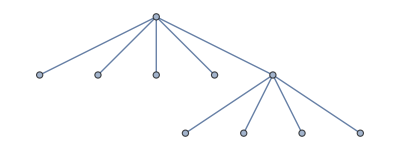
```mathematica
GraphRoots[-Graphics-]
S[k]//MatrixForm;
DeterminantD[-Graphics-]//Simplify
Det@S[k]//Simplify
NGraphRoots[-Graphics-]
NGraphRoots[-Graphics-,5]
NGraphEigenvalues[-Graphics-,5]

DeterminantD[moxx]//Simplify
Det@S[k]//Simplify
Det@S[k]/.{c1->1,c2->1,c3->1,c4->1}//Simplify
```

{{k→ConditionalExpression[18 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[9/2 π (-1+4 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[9/2 (π+4 π C[1]), C[1]∈ℤ]},{k→ConditionalExpression[9 (π+2 π C[1]), C[1]∈ℤ]},{k→ConditionalExpression[9 (ArcTan[3/4]+π (-1+2 C[1])), C[1]∈ℤ]},{k→ConditionalExpression[9 (π-ArcTan[3/4]+2 π C[1]), C[1]∈ℤ]},{k→ConditionalExpression[-9 ArcTan[3/4]+18 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[9 (ArcTan[3/4]+2 π C[1]), C[1]∈ℤ]}}

ⅇ^(-ⅈ k) (1+ⅇ^((2 ⅈ k)/9))^6 (-25+39 ⅇ^((2 ⅈ k)/9)-39 ⅇ^((4 ⅈ k)/9)+25 ⅇ^((2 ⅈ k)/3))

ⅇ^(-ⅈ k) (1+ⅇ^((2 ⅈ k)/9))^6 (-25+39 ⅇ^((2 ⅈ k)/9)-39 ⅇ^((4 ⅈ k)/9)+25 ⅇ^((2 ⅈ k)/3))

{{k→ConditionalExpression[56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-14.1372+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[14.1372+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[28.2743+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-22.4828+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[22.4828+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-5.79151+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[5.79151+56.5487 C[1], C[1]∈ℤ]}}

{0,5.79151,14.1372,22.4828,28.2743}

{0,33.5416,199.859,505.477,799.438}

4 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ (c1+c3+c4) k)/(c1+c2+c3+c4))) (-3-ⅇ^((2 ⅈ c2 k)/(c1+c2+c3+c4))+ⅇ^((ⅈ (c1+c3+c4) k)/(c1+c2+c3+c4))+3 ⅇ^((ⅈ (c1+2 c2+c3+c4) k)/(c1+c2+c3+c4)))

4 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ (c1+c3+c4) k)/(c1+c2+c3+c4))) (-3-ⅇ^((2 ⅈ c2 k)/(c1+c2+c3+c4))+ⅇ^((ⅈ (c1+c3+c4) k)/(c1+c2+c3+c4))+3 ⅇ^((ⅈ (c1+2 c2+c3+c4) k)/(c1+c2+c3+c4)))

4 ⅇ^(-ⅈ k) (3+ⅇ^((ⅈ k)/2)-4 ⅇ^((3 ⅈ k)/4)-4 ⅇ^((5 ⅈ k)/4)+ⅇ^((3 ⅈ k)/2)+3 ⅇ^(2 ⅈ k))

## Tests. My tests have been to compare with known results from literature and can be found below. The DeterminantD I get is often different from the ∑(k) which is given in the literature and differs by a complex k-dependent factor, A ⅇ^(-ⅈ k) where A is real, which never contributes with a root. There is ambiguity how to define ∑(k) as explained in Ref. 4. I call DeterminantD “my ∑(k)“ below. The crucial point is whether the eigenfrequencies and their multiplicities are the same as found in the literature. I find this to be true in all cases I have tested. I have also manually constructed the scattering matrices for three graphs in the paper: The references are: 1. Kennedy, J. B., Kurasov, P., Malenová, G., & Mugnolo, D. (2016). On the Spectral Gap of a Quantum Graph. Annales Henri Poincaré, 17(9), 2439–2473. also found at this link at the arXiv. 2. Malenova G. Diploma thesis https://physics.fjfi.cvut.cz/publications/mf/2009/malenova_thesis.pdf and one of her presentations. 3. Berkolaiko G. and Liu W. Simplicity of eigenvalues and non-vanishing of eigenfunctions of a quantum graph. Journal of Mathematical Analysis and Applications, 445(1):803–818, 2017. 4. Berkolaiko G. An elementary introduction to quantum graphs. https://arxiv.org/pdf/1603.07356.pdf 5. Blixt D. Master thesis. http://kodu.ut.ee/~blixt/Kandarb.pdf 6. Boris Gutkin and Uzy Smilansky. Can one hear the shape of a graph? Journal of Physics A: Mathematical and General, 34(31):6061, 2001. 7. Marlena Nowaczyk. Inverse Problems for Graph Laplacians. Centre for Mathematical Sciences, Lund University, 2007.

The following cells give the solution for the path graph which agrees with the results in Ref. 1 and 2


```mathematica
GraphRoots[-Graphics-,1]//Simplify//Expand
NGraphRoots[-Graphics-,3]
DeterminantD[-Graphics-] (* The multiplicities are one as they should be see Ref. 2 *)
```

{{k→ConditionalExpression[-2 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-π-2 π C[1], C[1]∈ℤ]}}

{0,3.14159,6.28319}

ⅇ^(-ⅈ k)-ⅇ^(ⅈ k)

The following cells give the solution for the loop graph which agrees with the results in Ref. 1 and 2


```mathematica
GraphRoots[-Graphics-,1]//Simplify//Expand
NGraphRoots[-Graphics-,3]
DeterminantD[-Graphics-]//Simplify (* The multiplicities are two for positive eigenfrequencies as they should be. See e. g. Ref. 2 *)
```

{{k→ConditionalExpression[6 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-2 π+6 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π+6 π C[1], C[1]∈ℤ]}}

{0,6.28319,12.5664}

-8 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

The following cells gives a comparison of my solution for a star graph with n leaves with the exact solution from Ref. 2. Full agreement is found also for the multiplicity.

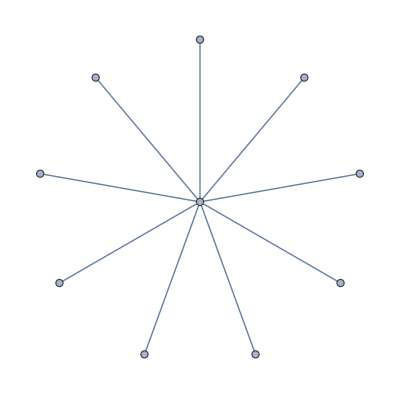
Small[-Graphics-]

{{k→ConditionalExpression[18 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(9 π)/2+18 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(9 π)/2+18 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[9 π+18 π C[1], C[1]∈ℤ]}}

-9 ⅇ^(-ⅈ k) (-1+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^8

{(9 π)/2+9 π C[1],9 π C[1]}

```mathematica
n=9;
h=StarGraph[n+1];
Small@h
GraphRoots[h]//Simplify//Expand
DeterminantD[h]//Simplify     (* The multiplicities are one and n-1 as they should be, see Ref. 2 *)

kstar1[p_,n_]:=π/2 n+p π n     (* Multiplicity n-1 *)
kstar2[p_,n_]:=n π p                (* Multiplicity one *)
{kstar1[C[1],n],kstar2[C[1],n]}
```

The following cell gives the eigenfrequency for the first non-trivial eigenvalue of the complete graph, given in Ref. 1, Eqn. 3.5. Full agreement is found.

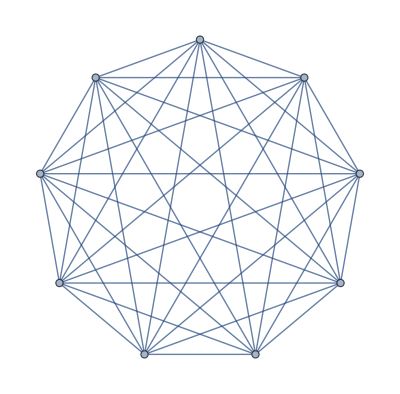
Small[-Graphics-]

{{k→ConditionalExpression[226.195 C[1], C[1]∈ℤ]},{k→ConditionalExpression[113.097+226.195 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-61.0605+226.195 C[1], C[1]∈ℤ]},{k→ConditionalExpression[61.0605+226.195 C[1], C[1]∈ℤ]}}

2048 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/36))^29 (1+ⅇ^((ⅈ k)/36))^27 (4+ⅇ^((ⅈ k)/36)+4 ⅇ^((ⅈ k)/18))^8

61.0605

```mathematica
n=9;  (* n is the number of vertices, feel free to change *)
h=CompleteGraph[n];
Small@h
GraphRoots[h]//Expand//N
DeterminantD[h]//Simplify (* I don't know if the multiplicities are right. Due to symmetry they should be high. *)
kcomplete[n_,L_]:=ArcCos[1/(1-n)]^2(n^2(n-1)^2)/(4 L^2)  (* This is the spectral gap, i. e. the second eigenvalue, according to Ref. 1. *)
kcomplete[n,1]^(1/2)//N//Simplify
```

The following cell gives the eigenfrequencies for the pumpkin graph with n edges. I get the same spectral gap as in Ref. 1.

```mathematica
n=7; (* n is the number of edges in the pumpkin graph *)
h=Graph@Flatten@Table[{1<->i,i<->20},{i,2,n+1}]; (* We insert an extra vertex on each edge. *)
Expand@GraphRoots[h]
NGraphRoots[h,2]  (* The numerical spectral gap *)
n π  (* This is the spectral gap given by Kennedy et al, which is n π where n is the number of edges. *)
DeterminantD[h]//Simplify
```

{{k→ConditionalExpression[28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-7 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[7 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[14 π+28 π C[1], C[1]∈ℤ]}}

{0,21.9911}

7 π

-6272 ⅇ^(-ⅈ k) (-1+ⅇ^((2 ⅈ k)/7))^7

The following cells compares my eigenfrequencies for the lasso graphs with the eigenfrequencies given by Berkolaiko in Ref. 4 Eqn. 48. I get the same ∑(k) as Berkolaiko apart form a factor which never contributes a root.

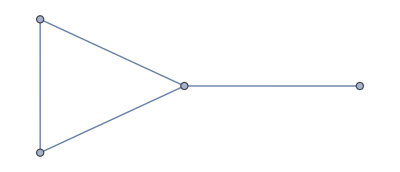
Small[-Graphics-]

{{k→ConditionalExpression[56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4.71239+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[4.71239+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-9.42478+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[9.42478+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-14.1372+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[14.1372+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-18.8496+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[18.8496+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-23.5619+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[23.5619+56.5487 C[1], C[1]∈ℤ]},{k→ConditionalExpression[28.2743+56.5487 C[1], C[1]∈ℤ]}}

48 Sin[k/3] Sin[(2 k)/3]

-4 ⅇ^(ⅈ k) Sin[k/3] Sin[(2 k)/3]

{{k→ConditionalExpression[9.42478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[4.71239+9.42478 C[1], C[1]∈ℤ]}}

{-18.8496,-14.1372,-9.42478,-4.71239,0.,4.71239,9.42478,14.1372,18.8496,23.5619}

{-80.1106,-75.3982,-70.6858,-65.9734,-61.2611,-56.5487,-51.8363,-47.1239,-42.4115,-37.6991,-32.9867,-28.2743,-23.5619,-18.8496,-14.1372,-9.42478,-4.71239,0.,4.71239,9.42478,14.1372,18.8496,23.5619,28.2743,32.9867,37.6991,42.4115,47.1239,51.8363,56.5487,61.2611,65.9734,70.6858,75.3982,80.1106,84.823}

```mathematica
L1=1/3;L2=2/3;  (* L2 is the total length of the loop, L1 is the length of the pendant. L1 + L2 = 1. *)
h=Graph[{1<->2,2<->3,3<->1,3<->4},EdgeWeight->{1/3 L2,1/3 L2,1/3 L2,L1}];
h//Small
myrules=GraphRoots[h]//N//Chop//FullSimplify
DeterminantD[h]//FullSimplify  (* This is the "∑(k)" I get *)

z1 = ⅇ^(ⅈ k L1);
z2 = ⅇ^(ⅈ k L2);
Sigmak=(1/3)(z2-1)(3 z1^2 z2-z1^2+z2-3);
Sigmak//FullSimplify//ExpToTrig//FullSimplify  (* This is the ∑(k)Berkolaiko gets in his eqn. 48 *)
berkolaikorules=Solve[Sigmak==0,k]//N//Simplify//Chop

Table[k/.berkolaikorules/.{C[1]->n},{n,-2,2}]//Flatten//Sort (* These are the numerical roots Berkolaiko gets *)
Table[k/.myrules/.{C[1]->n},{n,-1,1}]//Flatten//Sort (* These are the numerical roots I get *)
```

The following cells implement the isospectral graphs given in Marlena Nowaczyks thesis, Ref. 7, and by Boris Gutkin and Uzy Smilansky in Ref. 6. You can change a and b freely and check that they are isospectral using GraphRoots.

```mathematica
a=1;
b=3;
nowa1=({{∞, b, ∞, ∞, ∞, ∞, ∞, ∞}, {b, ∞, a, a, 2 a+2 b, ∞, ∞, ∞}, {∞, a, ∞, ∞, ∞, ∞, ∞, ∞}, {∞, a, ∞, ∞, ∞, ∞, ∞, ∞}, {∞, 2 a+2 b, ∞, ∞, ∞, b, a+2 b, 2 a+ b}, {∞, ∞, ∞, ∞, b, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, a+2 b, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, 2 a+ b, ∞, ∞, ∞}})
```

{{∞,3,∞,∞,∞,∞,∞,∞},{3,∞,1,1,8,∞,∞,∞},{∞,1,∞,∞,∞,∞,∞,∞},{∞,1,∞,∞,∞,∞,∞,∞},{∞,8,∞,∞,∞,3,7,5},{∞,∞,∞,∞,3,∞,∞,∞},{∞,∞,∞,∞,7,∞,∞,∞},{∞,∞,∞,∞,5,∞,∞,∞}}

```mathematica
nowa2=({{∞, a, ∞, ∞, ∞, ∞, ∞, ∞}, {a, ∞, b, 2a+3b, 2 a, ∞, ∞, ∞}, {∞, b, ∞, ∞, ∞, ∞, ∞, ∞}, {∞, 2a+3b, ∞, ∞, ∞, ∞, ∞, ∞}, {∞, 2 a, ∞, ∞, ∞, b, a+2 b, a}, {∞, ∞, ∞, ∞, b, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, a+2 b, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, a, ∞, ∞, ∞}})
```

{{∞,1,∞,∞,∞,∞,∞,∞},{1,∞,3,11,2,∞,∞,∞},{∞,3,∞,∞,∞,∞,∞,∞},{∞,11,∞,∞,∞,∞,∞,∞},{∞,2,∞,∞,∞,3,7,1},{∞,∞,∞,∞,3,∞,∞,∞},{∞,∞,∞,∞,7,∞,∞,∞},{∞,∞,∞,∞,1,∞,∞,∞}}

```mathematica
GraphRoots[nowa1]//N//Expand//Chop
```

{{k→ConditionalExpression[175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-21.9911+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[21.9911+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-43.9823+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[43.9823+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-65.9734+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[65.9734+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[87.9646+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[51.5296+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-36.4349+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-51.5296+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[36.4349+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[55.3257+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-32.6389+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-55.3257+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[32.6389+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[58.7591+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-29.2055+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-58.7591+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[29.2055+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[63.1364+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-24.8282+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-63.1364+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[24.8282+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[69.3174+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-18.6472+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-69.3174+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[18.6472+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[70.6145+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-17.3501+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-70.6145+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[17.3501+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[75.3245+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-12.6401+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-75.3245+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[12.6401+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[77.5255+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-10.4391+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-77.5255+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[10.4391+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[80.7641+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-7.20054+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-80.7641+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[7.20054+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[83.7431+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4.22147+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-83.7431+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[4.22147+175.929 C[1], C[1]∈ℤ]}}

```mathematica
GraphRoots[nowa2]//N//Expand//Chop
```

{{k→ConditionalExpression[175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-21.9911+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[21.9911+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-43.9823+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[43.9823+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-65.9734+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[65.9734+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[87.9646+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[51.5296+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-36.4349+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-51.5296+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[36.4349+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[55.3257+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-32.6389+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-55.3257+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[32.6389+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[58.7591+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-29.2055+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-58.7591+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[29.2055+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[63.1364+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-24.8282+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-63.1364+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[24.8282+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[69.3174+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-18.6472+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-69.3174+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[18.6472+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[70.6145+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-17.3501+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-70.6145+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[17.3501+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[75.3245+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-12.6401+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-75.3245+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[12.6401+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[77.5255+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-10.4391+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-77.5255+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[10.4391+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[80.7641+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-7.20054+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-80.7641+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[7.20054+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[83.7431+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4.22147+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-83.7431+175.929 C[1], C[1]∈ℤ]},{k→ConditionalExpression[4.22147+175.929 C[1], C[1]∈ℤ]}}

The following cells implement the flower-graph with two petals given in Daniel Blixt’s thesis, Ref. 5, as well as in Ref. 3 I get the same ∑(k) as Blixt apart from a factor which never contributes a root. I also get the same eigenvalues as Berkolaiko and Liu.

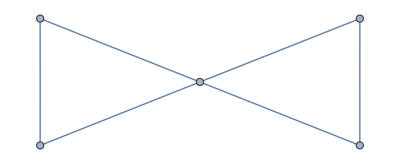
Small[-Graphics-]

{{k→ConditionalExpression[30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-2 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(5 π)/2+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(5 π)/2+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[4 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-5 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[5 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[6 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(15 π)/2+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(15 π)/2+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-8 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[8 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-10 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[10 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[12 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(25 π)/2+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(25 π)/2+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-14 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[14 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[15 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-12 π+30 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-6 π+30 π C[1], C[1]∈ℤ]}}

128 ⅈ (Sin[k/5]+Sin[(4 k)/5]-Sin[k])

Sin[k/10] Sin[(2 k)/5] Sin[k/2]

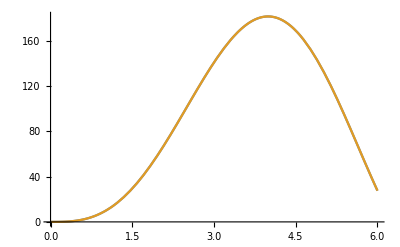

{{k→ConditionalExpression[94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-6.28319+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[6.28319+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-7.85398+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[7.85398+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-12.5664+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[12.5664+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-15.708+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[15.708+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[18.8496+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-23.5619+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[23.5619+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-25.1327+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[25.1327+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-31.4159+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[31.4159+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[37.6991+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-39.2699+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[39.2699+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-43.9823+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[43.9823+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[47.1239+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-37.6991+94.2478 C[1], C[1]∈ℤ]},{k→ConditionalExpression[-18.8496+94.2478 C[1], C[1]∈ℤ]}}

{-14.,-12.5,-12.,-10.,-8.,-7.5,-6.,-5.,-4.,-2.5,-2.,0.,2.,2.5,4.,5.,6.,7.5,8.,10.,12.,12.5,14.,15.,16.,17.5,18.,20.,22.,22.5,24.,25.,26.,27.5,28.,30.,32.,32.5,34.,35.,36.,37.5,38.,40.,42.,42.5,44.,45.,46.,47.5,48.,50.,52.,52.5,54.,55.,56.,57.5,58.,60.,62.,62.5,64.,65.,66.,67.5,68.,70.,72.,72.5,74.,75.}

{0,0,0,2,5/2,4,5,6,15/2,8,10,10,20,30,40}

```mathematica
k=.

l1=1/5;l2=1-l1;  (* l1 and l2 are the lengths of the individual petals and the total length should be one. *)
h=Graph[{1<->2,2<->3,3<->1,3<->4,4<->5,5<->3},EdgeWeight->{1/3 l1,1/3 l1,1/3 l1,1/3 l2,1/3 l2,1/3 l2}];
h//Small
GraphRoots[h]//Expand
Sig[k_]=DeterminantD[h]//FullSimplify  (* This is ∑(k) that I get, which will differ by a constant from Daniels ∑(k) *)

Sin[(k l1)/2]Sin[(k l2)/2]Sin[(k 1)/2]//FullSimplify (* This is ∑(k) as given by Daniel Blixt *)
(* Here we plot them and see that they are the same where the constant has been corrected to make them equal. You may check that their numerical difference is zero. *)
Plot[{Sig[k]//Im,512Sin[(k l1)/2]Sin[(k l2)/2]Sin[(k 1)/2]},{k,0,6}]
myrules=GraphRoots[h]//N//Chop//FullSimplify

berkolaikorules={{k->ConditionalExpression[(2 π C[1])/l1, C[1]∈Integers]},{k->ConditionalExpression[(2 π C[1])/l2, C[1]∈Integers]},{k->ConditionalExpression[(2 π C[1])/(l1+l2), C[1]∈Integers]}};
Table[k/.myrules/.{C[1]->n},{n,0,2}]/Pi//Flatten//Sort (* These are the numerical roots I get with Pi divided away. *)
Table[k/.berkolaikorules/.{C[1]->n},{n,0,4}]/Pi//Flatten//Sort (* These are the numerical roots Berkolaiko gets with Pi divided away. *)
```

The following cells implement the star graph with three leaves of unequal lengths comparing with the solution given by Berkolaiko in Ref. 4. I get the same ∑(k) as Berkolaiko apart from a factor which never contributes a root.


Small[-Graphics-]

2 ⅈ (Sin[(5 k)/18]-Sin[k/2]-Sin[(7 k)/9]-3 Sin[k])

2/3 (-ⅈ Cos[k]+Sin[k]) (-Sin[(5 k)/18]+Sin[k/2]+Sin[(7 k)/9]+3 Sin[k])

```mathematica
L1=1/9;L2=1/4;L3=1-L1-L2;
h=Graph[{1<->2,1<->3,1<->4},EdgeWeight->{L1,L2,L3}];
h//Small
GraphRoots[h];
Sig[k_]=DeterminantD[h]//Simplify//Expand//FullSimplify  (* This is ∑(k) that we get, which differs by a factor ⅈ/3(-ⅈ Cos[k]+Sin[k]), from Berkolaikos D(k) *)
z1 = ⅇ^(ⅈ k L1);
z2 = ⅇ^(ⅈ k L2);
z3 = ⅇ^(ⅈ k L3);
Sigmak=- z1^2 z2^2 z3^2 -1/3( z1^2 z2^2+z2^2 z3^2+z3^2 z1^2)+1/3( z1^2+z2^2+z3^2)+1;
Sigmak//FullSimplify//ExpToTrig//FullSimplify  (* This is the ∑(k) Berkolaiko gets in his eqn. 58*)
berkolaiko=Solve[Sigmak==0,k]//Simplify//Chop;
```

The following cell checks that GraphRoot scales the eigenfrequencies correctly when changing the length of the graph. See Ref. 1 for the correct scaling behaviour.

```mathematica
L1=1;L2=1;L3=2;
h=Graph[{1<->2,1<->3,1<->4},EdgeWeight->{L1,L2,L3}];
Small@h
GraphRoots[h,L] (* L is the total length of the graph *)
```

Small[-Graphics-]

{{k→ConditionalExpression[(4 π C[1])/L, C[1]∈ℤ]},{k→ConditionalExpression[(2 (π+2 π C[1]))/L, C[1]∈ℤ]},{k→ConditionalExpression[(2 (ArcTan[2 √2]+π (-1+2 C[1])))/L, C[1]∈ℤ]},{k→ConditionalExpression[(2 (π-ArcTan[2 √2]+2 π C[1]))/L, C[1]∈ℤ]}}

The following cell checks that deleting vertices with valence two does not change the eigenfrequencies. Only a few examples are given, feel free to test more.

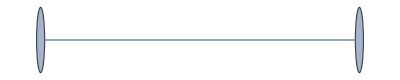
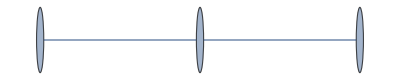
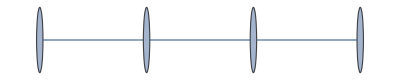
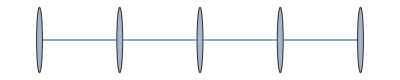
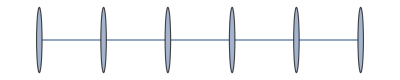
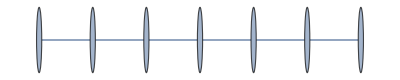
```mathematica
DeterminantD[-Graphics-]//Simplify
DeterminantD[-Graphics-]//Simplify
DeterminantD[-Graphics-]//Simplify 
DeterminantD[-Graphics-]//Simplify 
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}//FullSimplify 
{DeterminantD[({{∞, 1, ∞, ∞}, {1, ∞, 1, ∞}, {∞, 1, ∞, 1}, {∞, ∞, 1, ∞}})]//Simplify,WeightedAdjacencyGraph[({{∞, 1, ∞, ∞}, {1, ∞, 1, ∞}, {∞, 1, ∞, 1}, {∞, ∞, 1, ∞}}) ,VertexLabels->"Name", EdgeLabels->"EdgeWeight" ]}
 
{DeterminantD[({{∞, 2, ∞}, {2, ∞, 1}, {∞, 1, ∞}})]//Simplify,WeightedAdjacencyGraph[({{∞, 2, ∞}, {2, ∞, 1}, {∞, 1, ∞}}) ,VertexLabels->"Name", EdgeLabels->"EdgeWeight" ]}
```

64 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

-32 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

2048 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

128 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

{-2 ⅈ Sin[k],4 ⅈ Sin[k],-8 ⅈ Sin[k],16 ⅈ Sin[k],-32 ⅈ Sin[k],64 ⅈ Sin[k]}

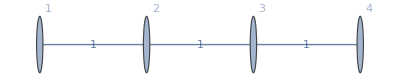
{-4 ⅇ^(-ⅈ k) (-1+ⅇ^(2 ⅈ k)),-Graphics-}

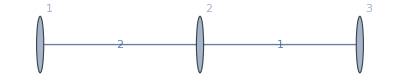
{2 ⅇ^(-ⅈ k) (-1+ⅇ^(2 ⅈ k)),-Graphics-}

The following cells checks DeterminantD and SDeterminantD against ScatteringDeterminantD where the latter secular determinant has been obtained by the scattering matrix approach described by Berkolaiko, Ref. 4.

```mathematica
ScatteringRoots[h_List|h_Graph,L_:1,solve_:1]:=Module[{n,s,t,m,mo,M,matn,eqns,vars,roots},Off[Part::pspec];Off[Part::pkspec1];
If[Head[w]==Graph,mo=(WeightedAdjacencyMatrix[w]//Normal)/.{0->∞},1];
If[Head[w]==List,mo=h,1];

Edges = 2 Length@EdgeList@h;
MyVertexDegree[w_Graph,{x_}|x_]:=VertexDegree[w,x];
MyEdgeList=EdgeList@DirectedGraph[h];
Sv=Array[0&,{ Edges,  Edges}];
MyEdgeList=Flatten@Gather[MyEdgeList,#1===Reverse[#2]&];
m=Table[Position[MyEdgeList[[j,2]]->_]@MyEdgeList,{j,1,Edges}];

Replacing[Sv_,i_]:=If[Length@m[[i]]>1,ReplacePart[m[[i]]->2/MyVertexDegree[h,MyEdgeList[[i,2]]]]@Sv[[i]],Sv[[i]]];
Sv=Table[Replacing[Sv,i],{i,1,Edges}];

Do[Sv[[i,i+1]]=2/MyVertexDegree[h,MyEdgeList[[i,2]]]-1,{i,1,Edges-1,2}];
Do[Sv[[i+1,i]]=2/MyVertexDegree[h,MyEdgeList[[i,1]]]-1,{i,1,Edges-1,2}];

Se=DiagonalMatrix[Table[Exp[ 2I k/Edges],{i, 1, Edges}]];
Sv//MatrixForm;
Se//MatrixForm;
Sigma=(IdentityMatrix[Edges]-Sv.Se)
]

ScatteringDeterminantD[h_List|h_Graph,L_:1,c1_:1,c2_:1,c3_:1,c4_:1,c5_:1,c6_:1]:=(ScatteringRoots[h,L,0];
Return[Det@Sigma//Simplify];);
```

```mathematica
Table[ScatteringDeterminantD@Allconnected[[j]]/SDeterminantD@Allconnected[[j]]//Simplify,{j,1,985}] (* This division should only give a numerical factor. In this formulation 985 cases will be tested, 
but you can add more. *)
```

```mathematica
Table[ScatteringDeterminantD@Allconnected[[j]]/DeterminantD@Allconnected[[j]]//Simplify,{j,1,985}] (* This division should only give a factor not contributing to a root, such as ⅇ^(ⅈ k). In this formulation 985 cases will be tested, but you can add more. *)
```